# Coral-algae model from Cunning et al 2017

## Numerics: ODE method, with 2 fluxes as state variables

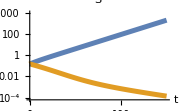
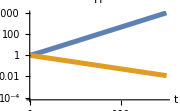
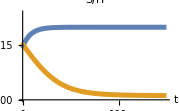
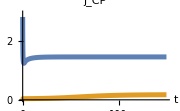
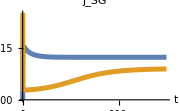

```mathematica
(*parameters*)
parvals={nNH->0.18,nNS->0.13,nNX->0.2,j0HT->0.03,j0ST->0.03,σNH->0.9,σCH->0.1,σNS->0.9,σCS->0.9,jXm->0.13,KX->1/1000000,jNm->0.035,KN->1.5*^-6,kCO2->10,jHGm->1,yCL->0.1,yC->0.8,astar->1.34,kNPQ->112,kROS->80,jCPm->2.8,jSGm->0.25,b->5,X->0,Ν->1.5*^-6,L->30,λ->10,tmax->150,S0->.15,H0->1};
(*choose which fluxes are state variables*)
fluxvars={jCP,jSG};
(*derived*)
(*SU*)
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);
rules={
jX->(jXm X)/(X+KX),
jN->(jNm Ν)/(Ν+KN),
jHT->j0HT,
rNS->σNS nNS j0ST,
jHG->F[jHGm][yC (ρC S/H+jX),(jN+nNX jX+rNH)nNH^-1],
jeC->jX-jHG/yC+(S ρC)/H,
jCO2->jeC kCO2,
jL->A astar L,
rCH->(jHT+(jHG (1-yC))/yC) σCH,
jeL->jL-jCP/yCL,
jNPQ->1/(1/jeL+1/kNPQ),
jST->(1+b cROS1) j0ST,
rNH->σNH nNH jHT,
A->1.256307+1.385969 E^(-6.479055 S/H),
rCS->σCS(j0ST+(1-yC)jSG yC^-1),
cROS1->Max[0,jeL-jNPQ]/kROS,
ρC->jCP-jSG yC^-1,
ρN->jN+jX nNX+rNH-jHG nNH,
jSG->F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS],
jCP->F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S]/(1+cROS1)
};
(*names of the state variables*)
names={jCP->"j_CP",jSG->"j_SG",S->"S",H->"H"};

simulate[pars_,fluxvars_,inivalues_]:=Module[{rulesnofluxvars,tsolve,states,eqs,inis},
rulesnofluxvars=Select[rules,Not[MemberQ[fluxvars,#[[1]]]]&];
(*list of states (fluxes) to track*)
(*format of elements in this list:*)
(*{ variable name, formula (aim for numerical implementation), initial guess (for numerical implementation) } *)  
tsolve=Select[rules,MemberQ[fluxvars,#[[1]]]&];
(*get all state variables*)
states=Join[fluxvars,{H,S}];
(*put together equations*)
eqs=(#[[1]]==(#[[2]]//.rulesnofluxvars/.((#->#[t])&/@states)))&/@Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])))&/@tsolve,
{
S'[t]==S(jSG-jST),
H'[t]==H(jHG-jHT)
}
];
(*set initial conditions*)
inis=(#[0]==(#/.inivalues))&/@states;
(*do the simulation (solve ODEs)*)
(NDSolve@@({Join[eqs/.pars,inis],#&/@states,{t,0,tmax},Method->Automatic}/.pars))[[1]]];
fontfamily="Times";
plotcols=ColorData[97]/@Range[2];
timeplotstyle={AxesOrigin->{0,0},ImageSize->Small,PlotStyle->({#,Thickness[.02]}&/@plotcols),AxesLabel->{"t"},LabelStyle->{FontFamily->fontfamily,FontSize->16},Ticks->{Charting`ScaledTicks[{Identity,Identity}][##,{4,4}]&,Automatic(*Charting`ScaledTicks[{Identity,Identity}][##,{3,3}]&*)}};
doplots[sols_,tmax_,maxSoverH_,minSandH_,maxSandH_]:=Style[Column[
{Row@Join[
(*plot S/H ratio*)

(*plot all state variables*)

Table[LogPlot[Evaluate[x[t]/.sols],{t,0,tmax},PlotLabel->(x/.{S->"S",H->"H"}),Evaluate@timeplotstyle,PlotRange->{minSandH,maxSandH}],{x,{S,H}}],
{Plot[Evaluate[{S[t]/H[t]}/.sols],{t,0,tmax},PlotLabel->"S/H",Evaluate@timeplotstyle,PlotRange->{0,maxSoverH}]}
],
Row@Table[Plot[Evaluate@Flatten@{Max[0,x[t]]/.sols},{t,0,tmax},PlotLabel->Style[x/.names,Italic],Evaluate@timeplotstyle,PlotRange->{x/.{jCP->{0,1.05jCPm},jSG->{0,jSGm}}/.parvals}],{x,fluxvars}]}
,Alignment->Center],LineBreakWithin->False];

sol1=simulate[parvals,fluxvars,{jSG->0,jCP->jCPm,H->H0,S->S0}/.parvals];
sol2=simulate[parvals,fluxvars,{jSG->jSGm,jCP->0,H->H0,S->S0}/.parvals];
(Export[NotebookDirectory[]<>"coral-simulation.pdf",#];#)&@doplots[{sol1,sol2},tmax/.parvals,.24,10^-4.2,10^4]
```

```mathematica
(Export[NotebookDirectory[]<>"coral-simulation-legend.pdf",#];#)&@Column[{
Style["Initializiation",FontFamily->fontfamily],
Grid[Table[Flatten@{Plot[1/2,{x,0,1},PlotRange->{0,1},PlotStyle->{Thickness[.15],plotcols[[i]]},Axes->None,ImageSize->20],Spacer[1],Style[#[[i]],FontFamily->fontfamily]&/@{{"j_CP(0) = j_CP_m    ","j_CP(0) = 0    "},{"j_SG(0) = 0","j_SG(0) = j_SG_m"}}},{i,2}],Alignment->Left]},Alignment->Center]
```

Initializiation
-Graphics- |  | j_CP(0) = j_CP_m     | j_SG(0) = 0
-Graphics- |  | j_CP(0) = 0     | j_SG(0) = j_SG_m

```mathematica
(*simulate model with different flux combinations, plot final S/H ratio*)
(*flux state variables choices to test*)
fluxvarss={{jCP,jSG}(*,{jCP,jHG},{jCP,ρC},{jCP,ρN}*)};
(*max value of ini fluxes in plot*)
maxiniflux={jCP->1.5,jSG->.25,jHG->.1,ρN->0.15,ρC->.5};
(*initial values for S and H*)
iniSH={S->S0,H->H0}/.parvals;
(*steps in horizontal and vertical direction of plot*)
steps=100;
(*parameter values, the same as before, but with higher tmax*)
tmax2=500;
parvals=parvals/.{(tmax->_)->(tmax->tmax2)};
```

```mathematica
(*function to make list of final values*)
Clear[SHlist];
SHlist[parvalues_,fluxvars_]:=SHlist[parvalues,fluxvars]=Flatten[ParallelTable[{x,y,S[tmax2]/H[tmax2]/.simulate[parvals,fluxvars,Join[iniSH,({#[[1]]->x,#[[2]]->y}&@fluxvars)]]},{x,0,fluxvars[[1]]/.maxiniflux,(fluxvars[[1]]/.maxiniflux)/steps},{y,0,fluxvars[[2]]/.maxiniflux,(fluxvars[[2]]/.maxiniflux)/steps}],1];
(*colors for plot*)
shadingcols=(ColorData[97]/@{1,2});
```

```mathematica
(Export[NotebookDirectory[]<>"coral-final-SH-legend.pdf",#];#)&@Style[Column[Join[(*{"S(t_max)/H(t_max)"}*){"Final S/H ratio"},Table[Row[{" ",shadingcols[[i]],NumberForm[{Min[#],Max[#]}[[i]],{3,3}]&@SHlist[parvals,fluxvarss[[1]]][[All,3]]},"    "],{i,2}]],Alignment->Left],FontFamily->fontfamily]
```

$Aborted

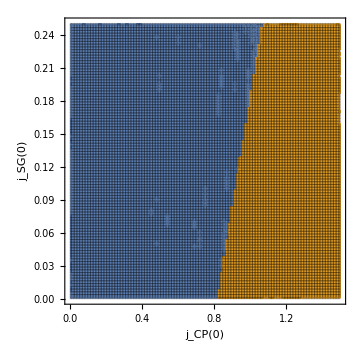

```mathematica
(*function for plot*)
iniplot[parvalues_,fluxvars_]:=(*ListContourPlot*)ListContourPlot[SHlist[parvalues,fluxvars],(*PlotRange->Full,*)FrameLabel->((#[0]&/@fluxvars)/.names),Contours->1,ContourShading->shadingcols,ImageSize->Medium,LabelStyle->16,Mesh->All,InterpolationOrder->0(*,MeshFunctions->{#1&,#2&}*),MeshStyle->{{Black,Opacity[.25]}}];
(*make the plots with the different flux choices, export to pdf*)
(Export[NotebookDirectory[]<>"coral-final-SH-1.pdf",#];#)&@iniplot[parvals,fluxvars]
```